```mathematica
f[x_]:=x*(1-x^2)+2;
a[x_]:= 1-x^2;
ϕ[x_,ϵ_]:=Sign[f[x]]*ϵ/(Integrate[1/(Abs[a[x]*u+2]),{u,x,x+ϵ}])
```

```mathematica
x0=107;
h=.01;
f[x0]
ϕ[x0,h]
Abs[(f[x0]-ϕ[x0,h])/f[x0]]
```

-1224934

-1.22499×10^6

0.0000467283

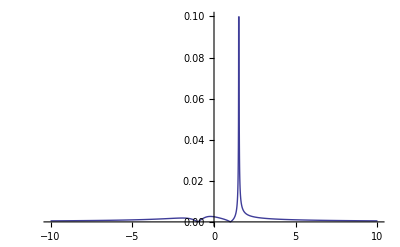

```mathematica
Plot[Abs[(f[x]-ϕ[x,h])/f[x]],{x,-10,10},PlotRange->{{-10,10},{0,.1}}]
```

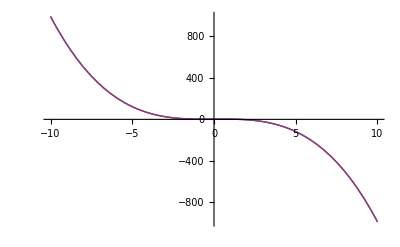

```mathematica
Plot[{f[x],ϕ[x,.01]},{x,-10,10}]
```